Exercises for Section 17 | Units

Convert 4.5 lbs (pounds) to kilograms. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[4.5 Quantity[, "Pounds"],"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[4.5, "Pounds"], "Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[4.5,"Pounds"],"Kilograms"]
```

2.04117 kg

Convert 60.25 mph to kilometers per hour. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Quantity[60.25,"Mph"],"Kph"]
```

96.963 km/h

```mathematica
UnitConvert[60.25 Quantity[, ("Miles")/("Hours")],"kph"]
```

96.963 km/h

Find the height of the Eiffel Tower in miles. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Entity["Building","EiffelTower::5h9w8"][EntityProperty["Building","Height"]],"Miles"]
```

0.201324 mi

Find the height of Mount Everest divided by the height of the Eiffel Tower. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["Mountain","MountEverest"][EntityProperty["Mountain","Elevation"]]/Entity["Building","EiffelTower::5h9w8"][EntityProperty["Building","Height"]]
```

27.3113

Find the mass of the Earth divided by the mass of the Moon. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]/Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]]
```

81.3

Convert 2500 Japanese yen to US dollars. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Quantity[2500, "Yen"],"$"]
```

22.69 $

Find the total of 35 ounces, 1/4 ton, 45 lbs and 9 stone in kilograms. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Quantity[35.0,"Ounce"]+Quantity[0.25,"Ton"]+Quantity[45.0,"lbs"]+Quantity[9.0,"Stone"],"kg"]
```

305.353 kg

Get a list of the distances to each planet using the "DistanceFromEarth" property, and convert all the results to light minutes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[EntityValue[EntityClass["Planet",All],"DistanceFromEarth"],"LightMinutes"]
```

{9.73991 light minutes,9.33487 light minutes,0. light minutes,21.8181 light minutes,33.4936 light minutes,75.2364 light minutes,160.831 light minutes,240.753 light minutes}

```mathematica
Entity["Planet","Planets"]
```

Entity[Planet,Planets]

```mathematica
PlanetData[Entity["Planet","Planets"],"AverageTemperature"]
```

Missing[UnknownEntity,{Planet,Planets}]

```mathematica
InputForm[EntityClass["Planet",All]]
```

"EntityClass[\"Planet\", All]"

Rotate the string "hello" by 180°. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Rotate["hello",180Degree]
```

hello

Make a table of a size-100 “A” rotated by 0° through 360° in steps of 30°. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Rotate[Style["A",100],n],{n,0Degree,360Degree,30Degree}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

Make a Manipulate to rotate an image of a cat between 0° and 180°. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Rotate[Entity["Species","Species:FelisCatus"][EntityProperty["Species","Image"]],d],{d,0Degree,180Degree}]
```

Generate graphics for a path obtained by turning 0°, 1°, 2°, ... , 180°. |

EXPECTED OUTPUT »

-Graphics- | ×

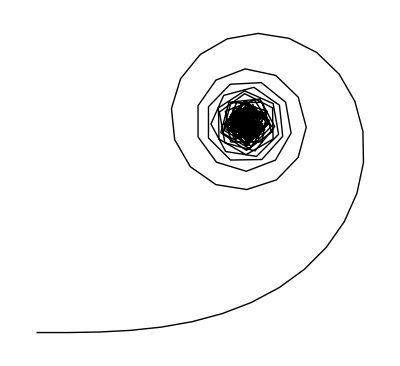

```mathematica
Graphics[Line[AnglePath[Table[a,{a,0Degree,180Degree,1Degree}]]]]
```

Make graphics of the path obtained by turning a constant angle 100 times, controlling the angle from 0° to 360° with a Manipulate. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics[Manipulate[Line[AnglePath[a]],{a,0Degree,360Degree}]];
Table[Table[a,{a,0,360,1}],100];

Graphics[Table[Line[AnglePath[{36Degree}]],100]];

Manipulate[Graphics[Line[AnglePath[a]]],{a,0Degree,360Degree,1Degree}];

Graphics[Table[Table[Line[AnglePath[a]],{a,1Degree,3Degree,1Degree}],5]];



Manipulate[Graphics[Line[AnglePath[Table[x, 100]]]], {x, 0, 360 °}];

Manipulate[Graphics[Line[AnglePath[Table[x,100]]]],{x,0,6Pi}]
```

AnglePath::steps: Invalid steps specification °.

AnglePath::steps: Invalid steps specification 2 °.

AnglePath::steps: Invalid steps specification 3 °.

General::stop: Further output of AnglePath::steps will be suppressed during this calculation.

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[x,100]]]],{x,0Degree,360Degree,1Degree}]
```

Make graphics of the path obtained by successively turning by the digits of 2^10000 multiplied by 30°. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

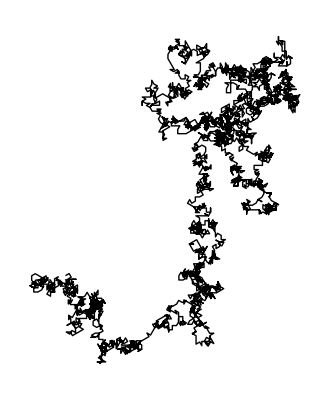

```mathematica
Graphics[Line[AnglePath[IntegerDigits[2^10000]*30Degree]]]
```

Convert 4.3 light years to furlongs. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Quantity[4.3,"Lightyears"],"Furlongs"]
```

2.02225×10^14 fur

Convert 20,000 leagues to miles. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Quantity[20000, "Leagues"], "Miles"]
```

60000 mi

Make a Manipulate to rotate a size-200 “W” to any angle from 0° to 360°. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Rotate[Style["W",200],a],{a,0Degree,360Degree}]
```

Rotate an image of the Great Pyramid by 180°. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Rotate[EntityClass["Great Pyramid","Image"],Pi]
```

```mathematica
EntityClass["Great Pyramid","Image"]
```

EntityClass[Great Pyramid,Image]

```mathematica
InputForm[GeoListPlot[{Entity["HistoricalSite","GreatPyramidOfGiza::kbgx6"]}]];
Rotate[EntityValue[Entity["Building","GreatPyramidOfGiza::jbm66"],"Image"],Pi]
```

-Graphics-

```mathematica
Rotate[EntityValue[Entity["Building","GreatPyramidOfGiza::jbm66"],"Image"],Pi]
```

-Graphics-

Generate a list of letters of the alphabet, each randomly rotated. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Characters[Alphabet[]];
```

```mathematica
Table[Rotate[Alphabet[],d],{d,0Degree,RandomInteger[{1,360}]Degree}];
```

```mathematica
Rotate[Table[letter,{letter}],x]
```

```mathematica
Table[Rotate[FromLetterNumber[x],RandomInteger[{1,180}]Degree],{x,1,26}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Generate graphics for a path obtained by turning 100 times through a random number of degrees between 0 and 360. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

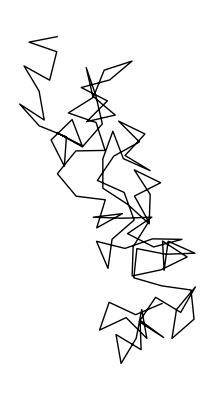

```mathematica
Graphics[Line[AnglePath[Table[RandomInteger[{0,360}]Degree,100]]]]
```